## Import Gillespie Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<Gillespie`
```

## Example: exponential decay

### Initial counts

```mathematica
cDict0=Association[];
cDict0["A"] =1000;
```

### Reactions

```mathematica
uniRxnList={
fMakeReaction["annihilation",0.5,{"A"},{}]
};
```

```mathematica
cDict0
```

```mathematica
{tSt,cDictSt,rxnCountSt}=fGillespie[10.0,0.1,cDict0,uniRxnList,{},{}];
```

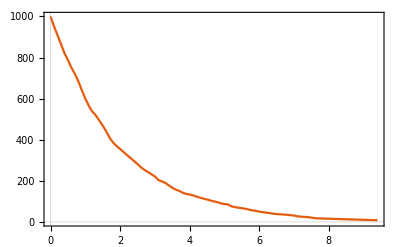

```mathematica
ListLinePlot[Transpose[{tSt,cDictSt["A"]}]]
```

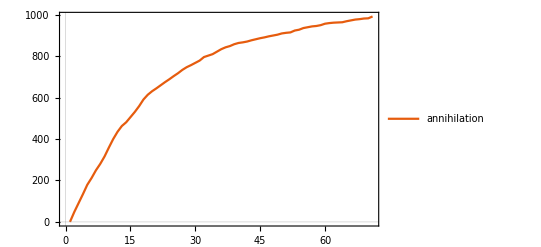

```mathematica
ListLinePlot[rxnCountSt,PlotLegends->Keys[rxnCountSt]]
```

## Example Rossler system

### Initial quantities

```mathematica
m=1;
```

```mathematica
x0q=1000*m;
y0q=8000*m;
z0q=10*m;
```

```mathematica
a1q=3000*m;
a2q=1*m;
a3q=1*m;
a4q=1650*m;
a5q=1000*m;
```

```mathematica
cDict0=Association[];
cDict0["A1"]=a1q;
cDict0["A2"]=a2q;
cDict0["A3"]=a3q;
cDict0["A4"]=a4q;
cDict0["A5"]=a5q;
cDict0["X"]=x0q;
cDict0["Y"]=y0q;
cDict0["Z"]=z0q;
```

### Reactions

```mathematica
km1=0.25;
km2=10^(-3);
km5=0.5;
kp1=1.0;
kp2=1.0;
kp3=1.0;
kp4=1.0;
kp5=1.0;
km3=1.0;
km4=1.0;
```

```mathematica
uniRxnList={
fMakeReaction["rm3",km3,{"A2"},{"A5","Y"}],
fMakeReaction["rm4",km4,{"A3"},{"X","Z"}]
};
```

```mathematica
biRxnList={
fMakeReaction["rp1",kp1,{"A1","X"},{"X","X"}],
fMakeReaction["rm1",km1,{"X","X"},{"A1","X"}],
fMakeReaction["rp2",kp2,{"X","Y"},{"Y","Y"}],
fMakeReaction["rm2",km2,{"Y","Y"},{"X","Y"}],
fMakeReaction["rp3",kp3,{"A5","Y"},{"A2"}],
fMakeReaction["rp4",kp4,{"X","Z"},{"A3"}],
fMakeReaction["rp5",kp5,{"A4","Z"},{"Z","Z"}],
fMakeReaction["rm5",km5,{"Z","Z"},{"A4","Z"}]
};
```

### Conservation laws

```mathematica
consLaws=<|"A1"->a1q,"A2"->a2q,"A3"->a3q,"A4"->a4q,"A5"->a5q|>;
```

### Run

```mathematica
{tSt,cDictSt,rxnCountSt}=fGillespie[0.1,0.0001,cDict0,uniRxnList,biRxnList,consLaws];
```

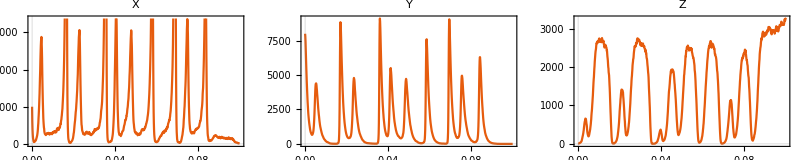

```mathematica
GraphicsRow[{
ListLinePlot[Transpose[{tSt,cDictSt["X"]}],PlotLabel->"X"],
ListLinePlot[Transpose[{tSt,cDictSt["Y"]}],PlotLabel->"Y"],
ListLinePlot[Transpose[{tSt,cDictSt["Z"]}],PlotLabel->"Z"]
},ImageSize->800]
```

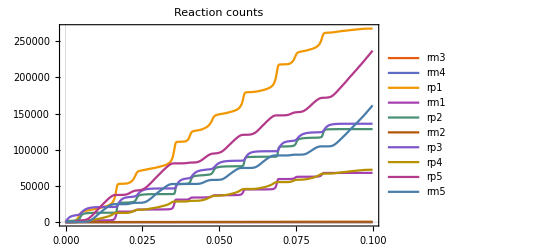

```mathematica
rxnCountStTimed=Table[Transpose[{tSt,rxnCountSt[k]}],{k,Keys[rxnCountSt]}];
ListLinePlot[rxnCountStTimed,PlotLegends->Keys[rxnCountSt],PlotLabel->"Reaction counts"]
```

```mathematica
dat=Transpose[{cDictSt["X"],cDictSt["Y"],cDictSt["Z"]}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

### PDE Soln

```mathematica
sol=NDSolve[
{
D[x[t],t]==x[t]*(a1q-km1*x[t]-z[t]-y[t])+km2*y[t]^2+a3q,
D[y[t],t]==y[t]*(x[t]-km2*y[t]-a5q)+a2q,
D[z[t],t]==z[t]*(a4q-x[t]-km5*z[t])+a3q,
x[0]==x0q,
y[0]==y0q,
z[0]==z0q
}
,{x[t],y[t],z[t]}
,{t,0,0.1}][[1]];
```

```mathematica
dat=Table[{x[t]/.sol,y[t]/.sol,z[t]/.sol},{t,0,0.1,0.0001}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

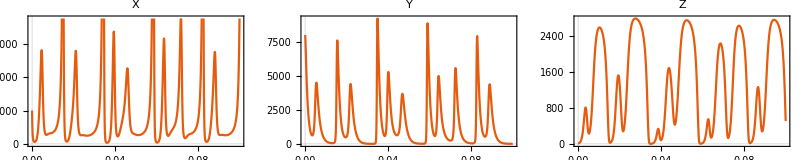

```mathematica
GraphicsRow[{
ListLinePlot[Table[{t,x[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"X"],
ListLinePlot[Table[{t,y[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"Y"],
ListLinePlot[Table[{t,z[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"Z"]
},ImageSize->800]
```

### Compare Gillespie to PDE

```mathematica
GraphicsRow[{
ListLinePlot[{Transpose[{tSt,cDictSt["X"]}],Table[{t,x[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"X"],
ListLinePlot[{Transpose[{tSt,cDictSt["Y"]}],Table[{t,y[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"Y"],
ListLinePlot[{Transpose[{tSt,cDictSt["Z"]}],Table[{t,z[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"Z",PlotLegends->{"Gillespie","PDE"}]
},ImageSize->800]
```

-Graphics-